```mathematica
u090494e　荒井直幸　2014年10月21日
```

```mathematica
Cycleplot[a_,b_,c_,d_,e_,f_,g_,h_,i_]:=ParametricPlot[{a Cos[d t+g]+b Cos[e t+h]+c Cos[f t+i],a Sin[d t+g]+b Sin[e t+h]+c Sin[f t+i]},{t,0,2Pi}]
```

-Graphics-

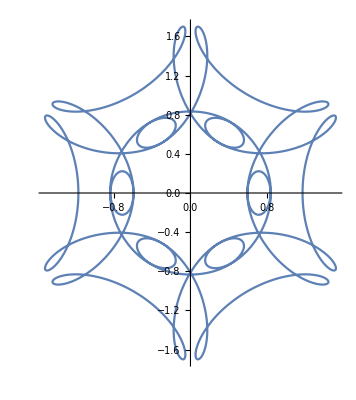

```mathematica
Cycleplot[1,1/2,1/3,1,7,-17,0,0,Pi]
```

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],u},{t,0,2 Pi},{u,0,4}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u*Sin[t],u*Cos[t],2*u},{t,0,2 Pi},{u,0,4}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u*Sin[t],u*Cos[t],t/3},{t,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u*Sin[t],u*Cos[t],t/3},{t,0,15},{u,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u] Cos[t],Sin[t] Cos[u],Sin[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t],Sin[2 t] Sin[u],Sin[2 t] Cos[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{2 Cos[u] Cos[t],2 Sin[t] Cos[u],Sin[u]},{t,0,2 Pi},{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
para1=ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}];
para2=ParametricPlot3D[{Sin[t],2 u,Cos[t]},{t,0,2 Pi},{u,-3,3}];
Show[para1,para2]
Show[para2,para1,PlotRange->{{-4,4},{-6,6},{-1,1}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3}]
```

-Graphics3D-

```mathematica
Plot3D[Exp[-x^2]Exp[-y^2],{x,-3,3},{y,-3,3},PlotRange->{0,1},AspectRatio->1]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,10},{y,0,10},PlotPoints->100]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[x-Sin[x],{x,0,4 Pi}]
RevolutionPlot3D[x-Sin[x],{x,0,2 Pi}]
RevolutionPlot3D[{2+Cos[x],2+Sin[x],x},{x,0,4 Pi}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
RevolutionPlot3D[{2+Cos[x],2+Sin[x],x},{x,0,4 π}]
```

-Graphics3D-

```mathematica
PolyhedronData["Tetrahedron"]PolyhedronData["Hexahedron"]
PolyhedronData["Octahedron"]PolyhedronData["Dodecahedron"]
PolyhedronData["Icosahedron"]
```

-Graphics3D- -Graphics3D-

-Graphics3D- -Graphics3D-

-Graphics3D-

```mathematica
今週の課題
```

```mathematica
graph1=ParametricPlot3D[{3 Cos[u] Cos[t],3 Sin[t] Cos[u],3 Sin[u]},{t,0,2 Pi},{u,0,2 Pi}];
graph2=ParametricPlot3D[{Sin[t],Cos[t],u},{t,0,2 Pi},{u,-20,20}];
graph3=ParametricPlot3D[{u,Sin[t],Cos[t]},{t,0,2 Pi},{u,-10,10}];
graph4=ParametricPlot3D[{Cos[t],u,Sin[t]},{t,0,2 Pi},{u,-10,10}];
graph5=ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}];
graph6=ParametricPlot3D[{Sin[u],Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u])},{t,0,2 Pi},{u,0,2 Pi}];
graph7=ParametricPlot3D[{Sin[t] (3+Cos[u]),Sin[u],Cos[t] (3+Cos[u])},{t,0,2 Pi},{u,0,2 Pi}];
graph8=ParametricPlot3D[{Cos[t] (10+Cos[u]),Sin[t] (10+Cos[u]),Sin[u]},{t,0,2 Pi},{u,0,2 Pi}];
graph9=ParametricPlot3D[{Sin[u],Cos[t] (10+Cos[u]),Sin[t] (10+Cos[u])},{t,0,2 Pi},{u,0,2 Pi}];
graph10=ParametricPlot3D[{Sin[t] (10+Cos[u]),Sin[u],Cos[t] (10+Cos[u])},{t,0,2 Pi},{u,0,2 Pi}];
graph11=ParametricPlot3D[{u Sin[t],u Cos[t],20},{t,0,2 Pi},{u,0,15}];
graph12=ParametricPlot3D[{u Sin[t],u Cos[t],26},{t,0,2 Pi},{u,0,15}];
graph13=ParametricPlot3D[{u Sin[t],u Cos[t],-20},{t,0,2 Pi},{u,0,15}];
graph14=ParametricPlot3D[{u Sin[t],u Cos[t],-26},{t,0,2 Pi},{u,0,15}];
graph15=ParametricPlot3D[{Cos[t] (15+Cos[u]),Sin[t] (15+Cos[u]),Sin[u]+21},{t,0,2 Pi},{u,0,2 Pi}];
graph16=ParametricPlot3D[{Cos[t] (15+Cos[u]),Sin[t] (15+Cos[u]),Sin[u]-21},{t,0,2 Pi},{u,0,2 Pi}];
graph17=ParametricPlot3D[{Cos[t] (15+Cos[u]),Sin[t] (15+Cos[u]),Sin[u]+23},{t,0,2 Pi},{u,0,2 Pi}];
graph18=ParametricPlot3D[{Cos[t] (15+Cos[u]),Sin[t] (15+Cos[u]),Sin[u]-23},{t,0,2 Pi},{u,0,2 Pi}];
graph19=ParametricPlot3D[{Cos[t] (15+Cos[u]),Sin[t] (15+Cos[u]),Sin[u]+25},{t,0,2 Pi},{u,0,2 Pi}];
graph20=ParametricPlot3D[{Cos[t] (15+Cos[u]),Sin[t] (15+Cos[u]),Sin[u]-25},{t,0,2 Pi},{u,0,2 Pi}];
graph21=ParametricPlot3D[{Sin[t]+13,Cos[t],u},{t,0,2 Pi},{u,-20,20}];
graph22=ParametricPlot3D[{Sin[t]-13,Cos[t],u},{t,0,2 Pi},{u,-20,20}];
graph23=ParametricPlot3D[{Sin[t],Cos[t]+13,u},{t,0,2 Pi},{u,-20,20}];
graph24=ParametricPlot3D[{Sin[t],Cos[t]-13,u},{t,0,2 Pi},{u,-20,20}];
graph25=ParametricPlot3D[{Cos[t] (1+Cos[u]),Sin[t] (1+Cos[u]),Sin[u]+20},{t,0,2 Pi},{u,0,2 Pi}];
graph26=ParametricPlot3D[{Cos[t] (1+Cos[u]),Sin[t] (1+Cos[u]),Sin[u]-20},{t,0,2 Pi},{u,0,2 Pi}];
graph27=ParametricPlot3D[{Sin[t] (5+Cos[u]),Sin[u],Cos[t] (5+Cos[u])+26},{t,0,2 Pi},{u,0,2 Pi}];
graph28=ParametricPlot3D[{Cos[t] (4+Cos[u])+6,Sin[t] (3+Cos[u]),Sin[u]+29},{t,0,2 Pi},{u,0,2 Pi}];
graph29=ParametricPlot3D[{Sin[t] (4+Cos[u])+12,Sin[u],Cos[t] (3+Cos[u])+30},{t,0,2 Pi},{u,0,2 Pi}];
graph30=ParametricPlot3D[{Cos[t] (4+Cos[u])+18,Sin[t] (3+Cos[u]),Sin[u]+29},{t,0,2 Pi},{u,0,2 Pi}];
graph31=ParametricPlot3D[{Sin[t] (3+Cos[u])+22,Sin[u],Cos[t] (4+Cos[u])+27},{t,0,2 Pi},{u,0,2 Pi}];
graph32=ParametricPlot3D[{Sin[u]+21,Cos[t] (3+Cos[u]),Sin[t] (4+Cos[u])+22},{t,0,2 Pi},{u,0,2 Pi}];
graph33=ParametricPlot3D[{Sin[t] (3+Cos[u])+20,Sin[u],Cos[t] (4+Cos[u])+17},{t,0,2 Pi},{u,0,2 Pi}];
graph34=ParametricPlot3D[{Sin[u]+20,Cos[t] (3+Cos[u]),Sin[t] (4+Cos[u])+11},{t,0,2 Pi},{u,0,2 Pi}];
graph35=ParametricPlot3D[{Sin[t] (3+Cos[u])+20,Sin[u],Cos[t] (4+Cos[u])+5},{t,0,2 Pi},{u,0,2 Pi}];
graph36=ParametricPlot3D[{Sin[u]+20,Cos[t] (3+Cos[u]),Sin[t] (4+Cos[u])-1},{t,0,2 Pi},{u,0,2 Pi}];
graph37=ParametricPlot3D[{Sin[t] (3+Cos[u])+20,Sin[u],Cos[t] (4+Cos[u])-7},{t,0,2 Pi},{u,0,2 Pi}];
graph38=ParametricPlot3D[{Sin[u]+20,Cos[t] (3+Cos[u]),Sin[t] (4+Cos[u])-13},{t,0,2 Pi},{u,0,2 Pi}];
graph39=ParametricPlot3D[{Sin[t] (3+Cos[u])+20,Sin[u],Cos[t] (4+Cos[u])-19},{t,0,2 Pi},{u,0,2 Pi}];
graph40=ParametricPlot3D[{Sin[u]+20,Cos[t] (3+Cos[u]),Sin[t] (4+Cos[u])-25},{t,0,2 Pi},{u,0,2 Pi}];
graph41=ParametricPlot3D[{Sin[t] (3+Cos[u])+20,Sin[u],Cos[t] (4+Cos[u])-31},{t,0,2 Pi},{u,0,2 Pi}];
graph42=ParametricPlot3D[{Sin[u]+20,Cos[t] (5+Cos[u]),Sin[t] (5+Cos[u])-38},{t,0,2 Pi},{u,0,2 Pi}];
graph43=ParametricPlot3D[{Sin[t] (10+Cos[u])+20,Sin[u]+(2 t)/(2 Pi)-1,Cos[t] (10+Cos[u])-50},{t,-Pi,3 Pi},{u,-Pi,3 Pi}];
graph44=ParametricPlot3D[{20,u Sin[t]+2,u Cos[t]-60},{t,0,2 Pi},{u,0,1}];
graph45=ParametricPlot3D[{20,u Sin[t]-2,u Cos[t]-60},{t,0,2 Pi},{u,0,1}];
Show[graph1,graph2,graph3,graph4,graph5,graph6,graph7,graph8,graph9,graph10,graph11,graph12,graph13,graph14,graph15,graph16,graph17,graph18,graph19,graph20,graph21,graph22,graph23,graph24,graph25,graph26,graph27,graph28,graph29,graph30,graph31,graph32,graph33,graph34,graph35,graph36,graph37,graph38,graph39,graph40,graph41,graph42,graph43,graph44,graph45,PlotRange->{{-50,50},{-50,50},{-65,65}}]
```

-Graphics3D-